# Mérés címe

```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{bm}"}];(*a kapcsos zárójelbe jönnek az include-álandó latex packagek vesszővel elválasztva, idézőjelek között*)
<<JLink`;InstallJava[];ReinstallJava[JVMArguments->"-Xmx1024m"]; 
Button["Start AutoSave",ScheduledTask[NotebookSave[EvaluationNotebook[]],60]](*ez a sor majd akkor kell ha a sablont elmentetted addig ki van kommentelve*)
<<LabDataProcess`
(*mathematica aktiválásához keygen: ibug.io/blog/2019/05/mathematica-keygen/*)
(*MaTeX package telepítéséhez: http://szhorvat.net/pelican/latex-typesetting-in-mathematica.html*)
```

Start AutoSave

```mathematica
Checkbox[x]
```

Checkbox[x]

## A kiértékelések előtt

```mathematica
ExtractArchive[FindFile["adatok.rar"]](*ez a sor kicsomagol bármilyen tömörített file-t*)
```

```mathematica
CsvMagic["/Users/herman/Downloads/Monte Carlo/NHF",".txt"," ","mc.xlsx",0](* ez a már sokat használt adatokat excelbe berakó függvény, célszerű a külömböző mérési feladatokat külömböző mappákba rakni és belőlük külömböző exceleket létrehozni*)
```

mc.xlsx

```mathematica
Separatorinator["/Users/szaszbence/Downloads/SmFeB/Bence/22.03.30","","	",";",".csv"](* Ezzel ki tudod egy mappában cserélni az adott file elválasztó jeleit. Ha már van olyan mappa amit létre akar hozni akkor nem fut le!!!*)
```

## Gyakran használt függvények

## Adatok ábrázolása

```mathematica
data={{{2,3},{1,3}},{{2,5},{1,4}}}
```

{{{2,3},{1,3}},{{2,5},{1,4}}}

```mathematica
{{{2,3},{1,3}},{{2,5},{1,4}}}
```

{{{2,3},{1,3}},{{2,5},{1,4}}}

```mathematica
ClearAll[data]
```

```mathematica
data[[1]]
```

{{2,3},{1,3}}

```mathematica
datas=MultiPlotDataMaker[colx_,coly_,path_,{sheets}]
```

### hibák ábrázolásához

```mathematica
dataserr=Around[data,hiba] (*ha minden x, y adatnak konstans hibája van*)
```

```mathematica
dataxhiba=Partition[Riffle[Around[Flatten[data][[1;;;;2]],hiba],Flatten[data][[2;;;;2]]],2]
datayhiba=Partition[Riffle[Flatten[data][[1;;;;2]],Around[Flatten[data][[2;;;;2]],hiba]],2]
```

```mathematica
datasxhiba=Partition[Riffle[Around[Flatten[data[[#]]][[1;;;;2]],hiba],Flatten[data[[#]]][[2;;;;2]]],2]&/@Range[Length[data]]
```

```mathematica
datasyhiba=Partition[Riffle[Flatten[data[[#]]][[1;;;;2]],Around[Flatten[data[[#]]][[2;;;;2]],hiba]],2]&/@Range[Length[data]]
```

{{{2,3hiba},{1,3hiba}},{{2,5hiba},{1,4hiba}}}

```mathematica
Length[data]
```

2

### ábárzolás

```mathematica
MultiPlot[datas,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

```mathematica
SpeedGrapher[xlsname_,xax_,yax_,{"xtengely","ytengely"}]
```

## Görbe illesztés

```mathematica
f=a*x+b;(*ez csak egy példa bármi lehet a függvény*)
co={{a,10},{b,-10},{c,-100}};(*illesztendő állandók a kezdő értékkel eggyütt, az nem feltétlen kell, lehet csak szimplán így is: {a,b,c}*)
vars=x;
rng={x,xmin,xmax};
FittingAutomaton[data,f,co,vars,rng,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

#### hibával

```mathematica
error=0.1
```

```mathematica
errors=ConstantArray[error,Length[data]]
xhiba={0.2,0.2,0.1}(*ha x nek van hibája y-nak nincs: yhiba=ConstantArray[0,Length[xhiba]], amúgy elég csak yhiba*)
yhiba={0.1,0.1,0.4}
```

```mathematica
errors=RootMeanSquare[#]&/@Partition[Riffle[xhiba,yhiba],2]
```

```mathematica
nlm=NonlinearModelFit[data,f,co,vars,MaxIterations->1000000,Weights->1/errors^2];

lp=ListPlot[data,Frame->True, PlotRange->All,PlotTheme->"Detailed",FrameLabel->MaTeX@{"xtengely","ytengely"},
PlotLegends->SwatchLegend[{ColorData[97,"ColorList"][[1]],Red},
MaTeX@{"adatsor","illesztés"},LegendFunction->ShadowBox],
Joined->False,  Epilog->First@Plot[nlm[x],rng,PlotStyle->Red]]

Print[nlm[{"BestFit","ParameterTable"}]];
```

## Mérés kiértékelése

```mathematica
path="/Users/herman/Downloads/Monte Carlo/NHF/mc_reduced_reduced.xlsx";
sheet =1 ;
colE = 1;
colc =2;
colp = 3;
colpair =4;
coltot=5;
```

```mathematica
En=Rest[ToExpression[Import[path,{"Data",sheet,All,colE}]]][[3;;]];
c=Rest[ToExpression[Import[path,{"Data",sheet,All,colc}]]][[3;;]];
p=Rest[ToExpression[Import[path,{"Data",sheet,All,colp}]]][[3;;]];
pair=Rest[ToExpression[Import[path,{"Data",sheet,All,colpair}]]][[3;;]];
tot=Rest[ToExpression[Import[path,{"Data",sheet,All,coltot}]]][[3;;]];
```

```mathematica
data={Partition[Riffle[En,c],2],Partition[Riffle[En,p],2],Partition[Riffle[En,pair],2],Partition[Riffle[En,tot],2]};
```

```mathematica
data[[4]]
```

{{0.0015,3801.01},{0.002,1917.02},{0.003,700.325},{0.004,335.133},{0.004557,658.537},{0.004702,616.638},{0.004852,771.939},{0.005,727.74},{0.005188,760.442},{0.006,529.747},{0.008,248.958},{0.01,137.567},{0.015,45.7841},{0.02,20.7146},{0.03,6.7137},{0.03317,29.869},{0.04,18.3527},{0.05,10.1757},{0.06,6.2279},{0.08,2.8625},{0.1,1.5764},{0.15,0.5663},{0.2,0.3019},{0.3,0.15341},{0.4,0.10996},{0.5,0.09035},{0.6,0.07901},{0.8,0.065708},{1.,0.057621},{1.022,0.056873},{1.25,0.0508634},{1.5,0.0464334},{2.,0.0411911},{2.044,0.0408625},{3.,0.0366762},{4.,0.0351151},{5.,0.0347177},{6.,0.0348291},{7.,0.0352586},{8.,0.0358371},{9.,0.0365101},{10.,0.0372152},{11.,0.0379613},{12.,0.0386873},{13.,0.0394329},{14.,0.040128},{15.,0.0408095},{16.,0.0414573},{18.,0.0426919},{20.,0.0438539}}

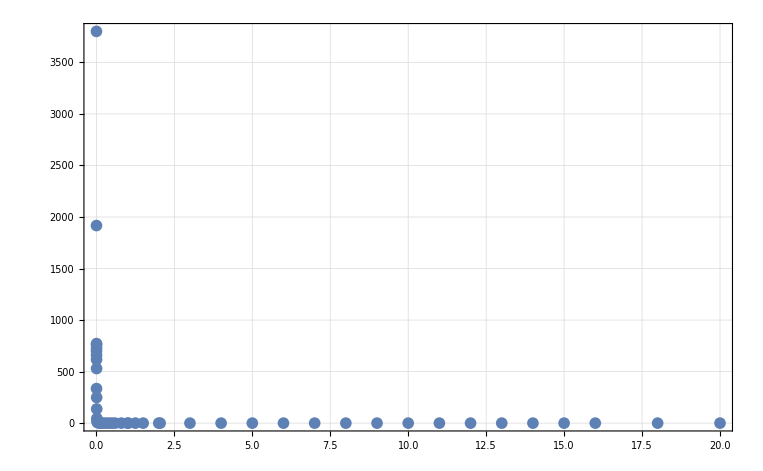

```mathematica
ListPlot[data[[4]], PlotRange->All,PlotTheme->"Detailed"]
```

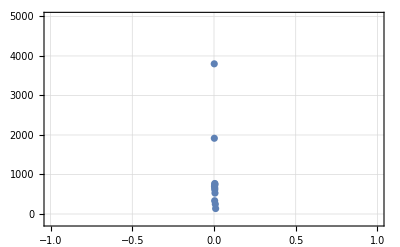

```mathematica
ListPlot[data[[2]][[;;12]], PlotRange->{{-1,1},{-200,5000}},PlotTheme->"Detailed"]
```

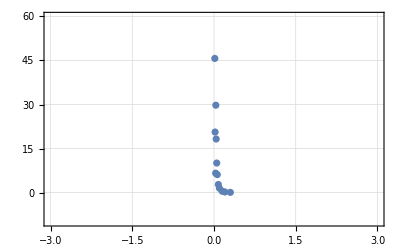

```mathematica
ListPlot[data[[2]][[12;;24]], PlotRange->{{-3,3},{-10,60}},PlotTheme->"Detailed",Epilog->First@Plot[f,{x,-1,1}]]
```

NonlinearModelFit::nrlnum: The function value {-3801.01-2.48959×10^-6 ⅈ,-1917.02-2.48959×10^-6 ⅈ,-700.324-2.48959×10^-6 ⅈ,-335.133-2.48959×10^-6 ⅈ,-658.537-2.48959×10^-6 ⅈ,-616.638-2.48959×10^-6 ⅈ,-771.939-2.48959×10^-6 ⅈ,-727.74-2.48959×10^-6 ⅈ,-760.441-2.48959×10^-6 ⅈ,-529.747-2.48959×10^-6 ⅈ,«40»} is not a list of real numbers with dimensions {50} at {a,b,cc} = {7.92462×10^-7,0.000108932,-213.22}.

{0.000108932-7.92462×10^-7 Log[-213.22+x], | Estimate | Standard Error | t-Statistic | P-Value
a | 7.92462×10^-7 | 299149.+1.98984×10^-11 ⅈ | 2.64905×10^-12-1.76207×10^-28 ⅈ | 1.+1.71469×10^-20 ⅈ
b | 0.000108932 | 1.89196×10^6+939803. ⅈ | 4.6181×10^-11-2.29397×10^-11 ⅈ | 1.+2.58319×10^-11 ⅈ
cc | -213.22 | 7.74599×10^13-0.206081 ⅈ | -2.75265×10^-12-7.32339×10^-27 ⅈ | 1.-1.12684×10^-19 ⅈ}

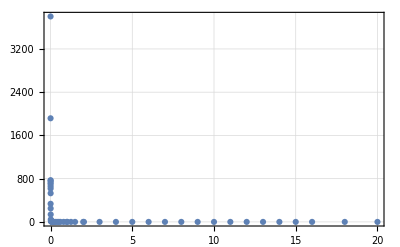

```mathematica
f=-a Log[x+cc]+b;(*ez csak egy példa bármi lehet a függvény*)
co={{a,0.000001},{b,0.000001},cc};(*illesztendő állandók a kezdő értékkel eggyütt, az nem feltétlen kell, lehet csak szimplán így is: {a,b,c}*)
vars=x;
rng={x,-0.000001,20};
FittingAutomaton[data[[4]],f,co,vars,rng,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

```mathematica
0.05942619569876138 Log[.5]
```

-0.0411911

```mathematica
f=Interpolation[data[[4]]]
```

InterpolatingFunction[…]

```mathematica
f[.5]
```

0.09035

```mathematica
data[[3]][[34]]
```

{2.044,0.002751}

{-5.6366×10^-6+0.000288361 x-0.00101928 x^2+0.000756567 x^3, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.000288361 | 0.000060578 | 4.76016 | 0.0000458252
b | -0.00101928 | 0.0000873425 | -11.67 | 1.11655×10^-12
cc | 0.000756567 | 0.0000300146 | 25.2066 | 9.5494×10^-22
d | -5.6366×10^-6 | 6.02696×10^-6 | -0.935232 | 0.357136}

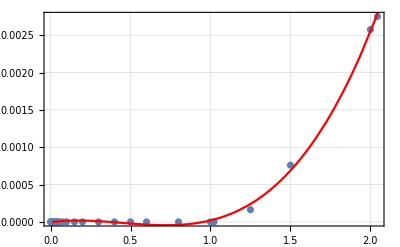

```mathematica
f=a x+b x^2 +cc x^3 +d ;(*ez csak egy példa bármi lehet a függvény*)
co={a,b,cc,d};(*illesztendő állandók a kezdő értékkel eggyütt, az nem feltétlen kell, lehet csak szimplán így is: {a,b,c}*)
vars=x;
rng={x,0.01,20};FittingAutomaton[data[[3]][[;;34]],f,co,vars,rng,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

```mathematica
data[[2]]
```

{{0.0015,3801.},{0.002,1917.},{0.003,700.3},{0.004,335.1},{0.004557,658.5},{0.004702,616.6},{0.004852,771.9},{0.005,727.7},{0.005188,760.4},{0.006,529.7},{0.008,248.9},{0.01,137.5},{0.015,45.7},{0.02,20.62},{0.03,6.607},{0.03317,29.76},{0.04,18.24},{0.05,10.06},{0.06,6.111},{0.08,2.746},{0.1,1.462},{0.15,0.4592},{0.2,0.2019},{0.3,0.06481},{0.4,0.02987},{0.5,0.01684},{0.6,0.01079},{0.8,0.005588},{1.,0.003491},{1.022,0.003323},{1.25,0.00224},{1.5,0.001604},{2.,0.0009761},{2.044,0.0009415},{3.,0.0005178},{4.,0.0003428},{5.,0.0002535},{6.,0.0002},{7.,0.0001647},{8.,0.0001398},{9.,0.0001212},{10.,0.0001069},{11.,0.00009565},{12.,0.00008648},{13.,0.00007888},{14.,0.00007249},{15.,0.00006706},{16.,0.0000624},{18.,0.00005472},{20.,0.00004873}}

```mathematica
f=InterpolatingPolynomial[data[[3]][[;;34]],x]
```

0.002751+(0.00134688+(0.00131789+(0.000801633+(-0.000298126+(-0.000534352+(0.0000761747+(0.00110465+(0.00125777+(0.00015104+(-0.00230209+(-0.00411226+(-0.0320319+(-0.0282864+(-0.0415828+(-0.0417895+(-0.0377943+(-0.0313472+(-0.0274863+(-0.0231797+(-0.0193142+(-0.0159859+(-0.00752393+(-0.434113+(13.3572+(-26732.2+(3.14496×10^6+(-6.9888×10^8+(4.6592×10^11+(-1.3312×10^14+(4.3546×10^16+(-1.18075×10^19+(3.68753×10^21-1.1001×10^24 (-0.004702+x)) (-0.005188+x)) (-0.004557+x)) (-0.005+x)) (-0.003+x)) (-0.006+x)) (-0.01+x)) (-0.002+x)) (-0.03317+x)) (-0.015+x)) (-0.05+x)) (-0.004+x)) (-0.03+x)) (-0.04+x)) (-0.08+x)) (-0.008+x)) (-0.1+x)) (-0.2+x)) (-0.5+x)) (-0.02+x)) (-1.+x)) (-0.3+x)) (-0.6+x)) (-0.06+x)) (-1.25+x)) (-0.8+x)) (-2.+x)) (-0.15+x)) (-1.5+x)) (-0.4+x)) (-1.022+x)) (-0.0015+x)) (-2.044+x)

```mathematica
data[[1]][[25]]
```

{0.08,0.1165}

```mathematica
-0.00005339204555150733+0.0014845048989619851/(-0.5857486933549776+0.98)
```

0.00371199

```mathematica
data[[1]][[1;;25]];
```

Divide::infy: Infinite expression -(1.00933×10^-165)/0. encountered.

Divide::infy: Infinite expression -(4.11913×10^-312)/0. encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

LinearAlgebra`BLAS`TRSV::mindet: Input matrix contains an indeterminate entry.

{-5.46306×10^-138-1.13328×10^-149 (10392.+x), | Estimate | Standard Error | t-Statistic | P-Value
a | -1.13328×10^-149 | 1.49303×10^-135 | -7.59044×10^-15 | 1
b | 10392. | 0. | ∞ | 0.
cc | -5.46306×10^-138 | 1.55155×10^-131 | -3.52102×10^-7 | 1.}

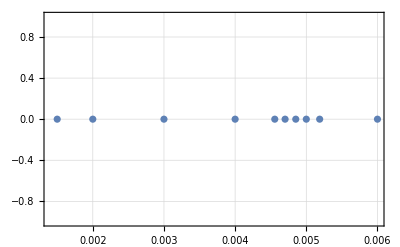

```mathematica
f=a*(x+b)+cc;(*ez csak egy példa bármi lehet a függvény*)
co={a,b,cc};(*illesztendő állandók a kezdő értékkel eggyütt, az nem feltétlen kell, lehet csak szimplán így is: {a,b,c}*)
vars=x;
rng={x,0.5,20};
FittingAutomaton[data[[3]][[;;10]],f,co,vars,rng,{"xtengely","ytengely"},{"a adatsor","b adatsor"}]
```

```mathematica
data[[2]]
```

{{0.001072,7924.},{0.0015,3801.},{0.002,1917.},{0.003,700.3},{0.004,335.1},{0.004557,238.7},{0.004557,658.5},{0.004702,616.6},{0.004852,577.4},{0.004852,771.9},{0.005,727.7},{0.005188,661.1},{0.005188,760.4},{0.006,529.7},{0.008,248.9},{0.01,137.5},{0.015,45.7},{0.02,20.62},{0.03,6.607},{0.03317,4.972},{0.03317,29.76},{0.04,18.24},{0.05,10.06},{0.06,6.111},{0.08,2.746},{0.1,1.462},{0.15,0.4592},{0.2,0.2019},{0.3,0.06481},{0.4,0.02987},{0.5,0.01684},{0.6,0.01079},{0.8,0.005588},{1.,0.003491},{1.022,0.003323},{1.25,0.00224},{1.5,0.001604},{2.,0.0009761},{2.044,0.0009415},{3.,0.0005178},{4.,0.0003428},{5.,0.0002535},{6.,0.0002},{7.,0.0001647},{8.,0.0001398},{9.,0.0001212},{10.,0.0001069},{11.,0.00009565},{12.,0.00008648},{13.,0.00007888},{14.,0.00007249},{15.,0.00006706},{16.,0.0000624},{18.,0.00005472},{20.,0.00004873}}

```mathematica
0.20841615674230948+0.031080392556373185* Log[0.02]
```

0.0868289

```mathematica
0.0491711772050159+0.12 (-0.4193214967799126+0.0377)^2
```

0.0666474

```mathematica
FindFit[data[[4]],- Log[b+cc x] +d,{a,b,cc,d},x]
```

FindFit::nrlnum: The function value {-3737.1-3.14159 ⅈ,-1853.1-3.14159 ⅈ,-636.411-3.14159 ⅈ,-271.219-3.14159 ⅈ,-594.623-3.14159 ⅈ,-552.724-3.14159 ⅈ,-708.025-3.14159 ⅈ,-663.826-3.14159 ⅈ,-696.527-3.14159 ⅈ,-465.832-3.14159 ⅈ,«40»} is not a list of real numbers with dimensions {50} at {a,b,cc,d} = {1.,-173.602,63.9884,69.0696}.

{a→1.,b→-173.602,cc→63.9884,d→69.0696}

```mathematica
fit=FindFormula[data[[4]],x,PerformanceGoal->"Quality",TargetFunctions->{Times, Log,Minus}]
```

FindFormula::nofun: {Times,Log,Minus} is not a non empty list of functions supported by FindFormula.

FindFormula[{{0.0015,3801.01},{0.002,1917.02},{0.003,700.325},{0.004,335.133},{0.004557,658.537},{0.004702,616.638},{0.004852,771.939},{0.005,727.74},{0.005188,760.442},{0.006,529.747},{0.008,248.958},{0.01,137.567},{0.015,45.7841},{0.02,20.7146},{0.03,6.7137},{0.03317,29.869},{0.04,18.3527},{0.05,10.1757},{0.06,6.2279},{0.08,2.8625},{0.1,1.5764},{0.15,0.5663},{0.2,0.3019},{0.3,0.15341},{0.4,0.10996},{0.5,0.09035},{0.6,0.07901},{0.8,0.065708},{1.,0.057621},{1.022,0.056873},{1.25,0.0508634},{1.5,0.0464334},{2.,0.0411911},{2.044,0.0408625},{3.,0.0366762},{4.,0.0351151},{5.,0.0347177},{6.,0.0348291},{7.,0.0352586},{8.,0.0358371},{9.,0.0365101},{10.,0.0372152},{11.,0.0379613},{12.,0.0386873},{13.,0.0394329},{14.,0.040128},{15.,0.0408095},{16.,0.0414573},{18.,0.0426919},{20.,0.0438539}},x,PerformanceGoal→Quality,TargetFunctions→{Times,Log,Minus}]

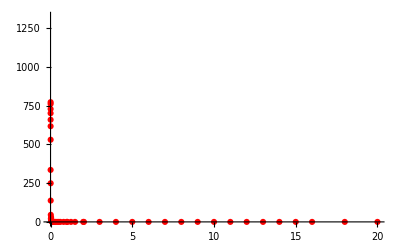

```mathematica
Show[ListPlot[data[[2]],PlotStyle->Red,PlotMarkers->Automatic],(*Plot the data*)Plot[fit,{x,Min[data[[2]][[All,1]]],Max[data[[2]][[All,1]]]},PlotStyle->Blue]  (*Plot the fitted function*)]
```

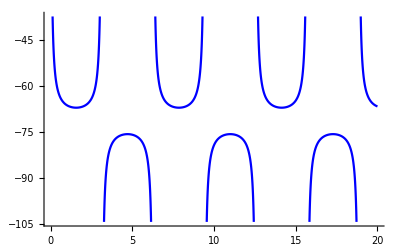

```mathematica
(*Plot the data*)Plot[fit,{x,Min[data[[2]][[All,1]]],Max[data[[2]][[All,1]]]},PlotStyle->Blue]
```

```mathematica
InterpolatingFunction
```

```mathematica
f =InterpolatingPolynomial[data[[2]],x];
```

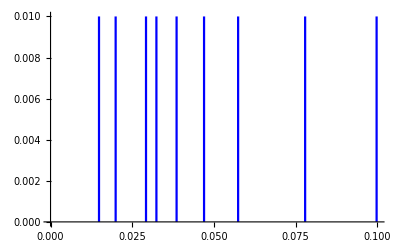

```mathematica
Plot[f,{x,Min[data[[2]][[All,1]]],Max[data[[2]][[All,1]]]},PlotStyle->Blue,PlotRange->{{0,0.1},{0,0.01}}]
```

```mathematica
fit[0.007811]
```

(30.8202+0.00888899/x^2)[0.007811]

```mathematica
30.820162833975502+0.00888898908499423/20^2
```

30.8202

```mathematica
interpolation=Interpolation[data[[2]]];  (*Perform the interpolation*)
Print["Interpolated function: ",interpolation]
```

Interpolated function: InterpolatingFunction[…]

```mathematica
interpolation[3.71]
```

0.000376257

```mathematica
f[0.00371];
```

```mathematica
data[[4]]
```

{{0.0015,3801.01},{0.002,1917.02},{0.003,700.325},{0.004,335.133},{0.004557,658.537},{0.004702,616.638},{0.004852,771.939},{0.005,727.74},{0.005188,760.442},{0.006,529.747},{0.008,248.958},{0.01,137.567},{0.015,45.7841},{0.02,20.7146},{0.03,6.7137},{0.03317,29.869},{0.04,18.3527},{0.05,10.1757},{0.06,6.2279},{0.08,2.8625},{0.1,1.5764},{0.15,0.5663},{0.2,0.3019},{0.3,0.15341},{0.4,0.10996},{0.5,0.09035},{0.6,0.07901},{0.8,0.065708},{1.,0.057621},{1.022,0.056873},{1.25,0.0508634},{1.5,0.0464334},{2.,0.0411911},{2.044,0.0408625},{3.,0.0366762},{4.,0.0351151},{5.,0.0347177},{6.,0.0348291},{7.,0.0352586},{8.,0.0358371},{9.,0.0365101},{10.,0.0372152},{11.,0.0379613},{12.,0.0386873},{13.,0.0394329},{14.,0.040128},{15.,0.0408095},{16.,0.0414573},{18.,0.0426919},{20.,0.0438539}}

```mathematica
sy=Interpolation[{{1.0,2.0},{2.0,3.0},{3.0,5.0},{4.0,8.0},{5.0,10.0}}]
```

InterpolatingFunction[…]

```mathematica
sy[2.5]
```

3.875